# Setup

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["C:\\Users\\Miguel\\Github\\libs\\QMB\\Kernel\\init.m"];
```

```mathematica
(*Get["C:\\Users\\Miguel\\Github\\Spin transport\\Quantum channel\\QMB_offline.wl"];*)
```

```mathematica
LaunchKernels[12];
```

```mathematica
Names["QMB`*"]
```

{AnalyticalNumberVarianceGOE,AnalyticalNumberVarianceGUE,AnalyticalNumberVariancePoisson,ARQMHamiltonian,BlochVector,BoseHubbardHamiltonian,BoseHubbardHilbertSpaceDimension,BosonEscapeKrausOperators,BosonicPartialTrace,Braket,ClassicalMapeo,ClassicalStep,ClassicalToDisk,ClassicalToSphere,COEAsymptoticSigma2,COESFFAnalytical,coherentstate,CommutationQ,CompileLevelCounter,CompileSFF,ComplexSpacingRatios,ComplexToPolar,ComputeSigma2Sliding,Concurrence,DensityMatrix,Dyad,EigenvectorQ,EmpiricalKLDivergence,EnsembleSFF,EnsembleSigma2,EvaluateSpectrumSigma2,FixCkForStateEvoultion,Floq,Floqb,Floqbn,Floqn,Floqsym,FluctuationPowerSpectrum,FockBasis,FockBasisIndex,FockBasisStateAsColumnVector,FuzzyMeasurement,FuzzyMeasurementChannel,GenerateCOEEnsemble,generateCoherentStateCompiler,GenerateGinibreMatrix,GenerateQKTEnsemble,generateSpinOperators,GetFluctuations,GetQKTParityEigensystem,GetQKTParitySpectra,HaarRandomState,HilbertSpaceDim,InitializationBosonicPartialTrace,InitializeVariables,IntWignerCOE,IPR,KetInComputationalBasisFromVector,KineticTermBoseHubbardHamiltonian,KLDivergence,KroneckerVectorProduct,kthOrderSpacings,LengthSpectrum,LevelSpacingDistribution,MatrixCommutator,MatrixPartialTrace,MatrixPartialTraceFromPureState,MeanLevelSpacingRatio,MutuallyCommutingSetQ,NNSpacings,NormalizedSpacingRatios,NumberVariance,ParitySectorIndices,PartialTranspose,Pauli,PoolSpacingRatios,PoolSpacings,PotentialTermBoseHubbardHamiltonian,PrCOE,PrCUE,PrPoisson,Purity,QuantumTexture,Qubit,QubitStateFromBlochVector,RandomChainProductState,RandomCOESpectrum,RandomQubitState,RandomSU2Parameters,RandomSU2Rotation,RatiosDistribution,RatiosDistributionPoisson,RenyiEntropy,Reshuffle,SingleSFF,SingleSpectrumSigma2,SortFockBasis,SpacingRatios,SpectralFormFactor,SpectralFormFactorRMT,StateEvolution,SU2Rotation,SU2RotationParameters,SuperoperatorFromU,SwapMatrix,SymmetricSubspace,Tag,TimeAveragedSFF,Unfold,UnfoldLinear,ValidateUnfolding,VectorFromKetInComputationalBasis,WeylMatrix,WignerCOE,ω}

# Definitions

```mathematica
(* ================================================================ *)
(* BLOCK 0 – Kernel setup                                           *)
(* ================================================================ *)
(* Set compile target for all Compile calls in this session.        *)
(* Falls back to "WVM" automatically if no C compiler is found.     *)
$CompileTarget = "C";

(* ================================================================ *)
(* BLOCK 1 – Compiled partial traces (hardcoded for 4x4 ρ_AB)      *)
(* *)
(* These are exact index operations on a 4x4 complex matrix.        *)
(* Layout assumed: rows/cols indexed as (q1,q2) ∈ {00,01,10,11}.   *)
(* ================================================================ *)
Clear[TraceOutA,TraceOutB];
TraceOutB = Compile[                  (* keep spin A, trace out B *)
  {{ρ, _Complex, 2}},
  {{ρ[[1,1]] + ρ[[2,2]],  ρ[[1,3]] + ρ[[2,4]]},
   {ρ[[3,1]] + ρ[[4,2]],  ρ[[3,3]] + ρ[[4,4]]}},
  CompilationTarget -> $CompileTarget,
  RuntimeOptions -> "Speed"
];
TraceOutA = Compile[                  (* keep spin B, trace out A *)
  {{ρ, _Complex, 2}},
  {{ρ[[1,1]] + ρ[[3,3]],  ρ[[1,2]] + ρ[[3,4]]},
   {ρ[[2,1]] + ρ[[4,3]],  ρ[[2,2]] + ρ[[4,4]]}},
  CompilationTarget -> $CompileTarget,
  RuntimeOptions -> "Speed"
];

(* ================================================================ *)
(* BLOCK 2 – Von Neumann entropy                                     *)
(* *)
(* 2×2: compiled with analytical eigenvalues – no Eigenvalues call. *)
(* Eigenvalues of {{a,b},{c,d}} with a,d real and c=Conj[b]:        *)
(* λ_{1,2} = ((a+d) ± sqrt((a-d)^2 + 4|b|^2)) / 2                  *)
(* *)
(* 4×4: cannot be compiled – Eigenvalues[] is not compilable.       *)
(* Called once per time step on a 4×4 matrix – cost is negligible. *)
(* ================================================================ *)
Clear[VNEntropy2x2,VNEntropy4x4];
VNEntropy2x2 = Compile[
  {{ρ, _Complex, 2}},
  Module[{r11, r22, r12r, r12i, absq, disc, λ1, λ2},
    r11  = Re[ρ[[1,1]]];
    r22  = Re[ρ[[2,2]]];
    r12r = Re[ρ[[1,2]]];
    r12i = Im[ρ[[1,2]]];
    absq = r12r^2 + r12i^2;               (* |ρ12|^2 – never negative *)
    disc = Sqrt[(r11 - r22)^2 + 4.*absq]; (* sqrt arg always ≥ 0     *)
    λ1   = (r11 + r22 + disc)/2.;
    λ2   = (r11 + r22 - disc)/2.;
    If[λ1 > 1.*^-14, -λ1*Log[λ1], 0.] +
    If[λ2 > 1.*^-14, -λ2*Log[λ2], 0.]
  ],
  CompilationTarget -> $CompileTarget,
  RuntimeOptions -> "Speed"
];
VNEntropy4x4[ρ_] := Module[
  {λ = Select[Re[Eigenvalues[N[ρ]]], # > 1.*^-14 &]},
  -λ . Log[λ]
];

(* ================================================================ *)
(* BLOCK 3 – Concurrence (Wootters 1998)                            *)
(* *)
(* spinFlip = σy⊗σy is constant – precomputed once here as a        *)
(* packed numerical array so Dot calls use BLAS.                    *)
(* Eigenvalues on 4x4 is not compilable; the 4x4 call is trivial.   *)
(* ================================================================ *)
spinFlip = N[KroneckerProduct[PauliMatrix[2], PauliMatrix[2]]];

Clear[Concurrence];
Concurrence[ρ_] := Module[
  {ρTilde, λs},
  ρTilde = spinFlip . Conjugate[ρ] . spinFlip;
  λs     = Reverse[Sort[Re[Sqrt[Chop[Eigenvalues[ρ . ρTilde]]]]]];
  Max[0., λs[[1]] - λs[[2]] - λs[[3]] - λs[[4]]]
];

(* ================================================================ *)
(* BLOCK 4 – Single-pass observable aggregator                      *)
(* *)
(* Takes the 4×4 ρ_AB and a reference state ρ_ref (for survival).  *)
(* All quantities computed in one pass over ρ_AB – no redundancy.   *)
(* ================================================================ *)
Clear[ComputeAllObservables];
ComputeAllObservables[ρAB_, ρref_] := Module[
  {ρA, ρB, SA, SB, SAB},
  ρA  = TraceOutB[ρAB];
  ρB  = TraceOutA[ρAB];
  SA  = VNEntropy2x2[ρA];
  SB  = VNEntropy2x2[ρB];
  SAB = VNEntropy4x4[ρAB];
  <|
    "Concurrence"  -> Concurrence[ρAB],
    "Purity"       -> Re[Tr[ρAB . ρAB]],
    "EntropyA"     -> SA,
    "EntropyB"     -> SB,
    "MutualInfo"   -> SA + SB - SAB,       (* I(A:B) = S(A)+S(B)-S(AB) *)
    "SpinSurvival" -> Re[Tr[ρref . ρAB]]   (* valid for pure ρref      *)
  |>
];

(* ================================================================ *)
(* BLOCK 5 – Wavefunction Utilities                                 *)
(* *)
(* BuildInitialStateVector creates a pure state vector for the full  *)
(* [Q1, Chain, Q2] system layout from separate subsystems.           *)
(* GetRhoAB performs an ultra-fast partial trace extraction of the   *)
(* 4x4 reduced density matrix of the boundary spins directly from   *)
(* the pure state wavefunction.                                      *)
(* ================================================================ *)
Clear[BuildInitialStateVector, GetRhoAB];
BuildInitialStateVector[psiAB_List, psiChain_List, L_] := Module[{tensor},
  (* psiAB is a length-4 vector; psiChain is a length-2^L vector *)
  (* Reshape system spins to 2x2, take tensor product with chain -> shape {2, 2, 2^L} *)
  tensor = TensorProduct[ArrayReshape[psiAB, {2, 2}], psiChain];
  (* Permute from (q1, q2, c) to match your layout (q1, c, q2), then flatten *)
  Flatten[Transpose[tensor, {1, 3, 2}]]
];

GetRhoAB[psi_, L_] := Module[{M},
  (* psi is a 2^(L+2) position-basis vector with layout (q1, c, q2) *)
  (* Reshape to 3D, permute indices to (q1, q2, c), and flatten system dimensions to 4 *)
  M = ArrayReshape[
    Transpose[ArrayReshape[psi, {2, 2^L, 2}], {1, 3, 2}],
    {4, 2^L}
  ];
  (* A pure state partial trace reduces exactly to M . M^Dagger *)
  M . ConjugateTranspose[M]
];

(* ================================================================ *)
(* BLOCK 6 – Pauli operators                                        *)
(* Packed numerical arrays – no symbolic overhead anywhere          *)
(* ================================================================ *)
σx  = N[PauliMatrix[1]];
σy  = N[PauliMatrix[2]];
σz  = N[PauliMatrix[3]];
σp  = σx + I*σy;   (* raising  operator *)
σm  = σx - I*σy;   (* lowering operator *)
id2 = N[IdentityMatrix[2]];

(* ================================================================ *)
(* BLOCK 7 – Hamiltonian embedding functions                       *)
(* *)
(* All operators live in the full [Q1, Chain, Q2] Hilbert space.    *)
(* SparseArray identities keep construction memory-efficient.       *)
(* Normal[] called only once at diagonalization – not here.         *)
(* ================================================================ *)
Clear[SparseId,EmbedSpinA,EmbedSpinB,EmbedChain,EmbedChainSite];
SparseId[n_] := SparseArray[Band[{1, 1}] -> 1., {n, n}];

(* Embed a 2x2 operator at spin A position in the full space *)
EmbedSpinA[op_, L_] :=
  KroneckerProduct[op, SparseId[2^L], SparseId[2]];
(* Embed a 2x2 operator at spin B position in the full space *)
EmbedSpinB[op_, L_] :=
  KroneckerProduct[SparseId[2], SparseId[2^L], op];
(* Embed the full chain Hamiltonian block in the full space *)
EmbedChain[Ha_, L_] :=
  KroneckerProduct[SparseId[2], Ha, SparseId[2]];
(* Embed a 2x2 operator at site k (1-indexed) within the chain     *)
EmbedChainSite[op_, k_, L_] :=
  KroneckerProduct[SparseId[2^(k - 1)], op, SparseId[2^(L - k)]];

(* ================================================================ *)
(* BLOCK 8 – Boundary coupling constructors                        *)
(* *)
(* Takes a list of {opLeft, opRight} pairs and coupling strength.   *)
(* A-chain couples spin A to the FIRST chain site.                  *)
(* B-chain couples spin B to the LAST  chain site.                  *)
(* ================================================================ *)
Clear[BuildCouplingAChain, BuildCouplingBChain];

BuildCouplingAChain[couplingTerms_, L_] := Sum[
  term[[1]] * KroneckerProduct[
    term[[2]],
    KroneckerProduct[term[[3]], SparseId[2^(L - 1)]],
    SparseId[2]
  ],
  {term, couplingTerms}
];

BuildCouplingBChain[couplingTerms_, L_] := Sum[
  term[[1]] * KroneckerProduct[
    SparseId[2],
    KroneckerProduct[SparseId[2^(L - 1)], term[[2]]],
    term[[3]]
  ],
  {term, couplingTerms}
];

(* ================================================================ *)
(* BLOCK 9 – Full Hamiltonian assembler and diagonalization        *)
(* *)
(* Returns {eigenvalues (D-vector), eigenvectors (D[Times]D, rows=vecs)}  *)
(* ================================================================ *)
Clear[BuildFullHamiltonian,DiagonalizeH];
BuildFullHamiltonian[HAlocal_, Ha_, HBlocal_, couplingA_, couplingB_, L_] :=
  EmbedSpinA[HAlocal, L] +
  EmbedChain[Ha, L]        +
  EmbedSpinB[HBlocal, L]  +
  BuildCouplingAChain[couplingA, L] +
  BuildCouplingBChain[couplingB, L];

DiagonalizeH[HT_] := Transpose[Sort[Transpose[Eigensystem[Normal[N[HT]]]]]];

(* DISTRIBUTE – send core definitions to parallel kernels            *)
DistributeDefinitions[
  σx, σy, σz, σp, σm, id2, spinFlip,
  TraceOutA, TraceOutB, VNEntropy2x2, VNEntropy4x4, Concurrence,
  ComputeAllObservables, GetRhoAB
];
```

# Method

## Parameters

```mathematica
(* ================================================================ *)
(* MODEL + STATE SPECIFICATION                                      *)
(* ================================================================ *)
(* --- System size --- *)
L=7;
{Δa,Δb,λa,λb}={1.,1.,0.1,0.1};
```

```mathematica
(* --- Local Hamiltonians for the two system spins ---             *)
HAlocal = Δa * σz;       (* 2x2, field on spin A *)
HBlocal = Δb * σz;       (* 2x2, field on spin B *)
(* --- Boundary coupling terms ---                                  *)
couplingA={{λa,σp,σm},{λa,σm,σp}};
couplingB={{λb,σp,σm},{λb,σm,σp}};
```

```mathematica
?XXZwLocalDefectHamiltonian
```

```mathematica
{Jxy,Jz,w,ed,d}={1.,0.01,0.,0.,L};
```

```mathematica
(* --- Chain Hamiltonian (Your custom built-in function implementation) --- *)
Ha = XXZwLocalDefectHamiltonian[Jxy, Jz, w, ed, L, d];
(* --- Build and diagonalize the full Hamiltonian --- *)
HT             = Chop[BuildFullHamiltonian[HAlocal, Ha, HBlocal, couplingA, couplingB, L]];
{Eval, Evec}   = DiagonalizeH[HT];
```

0.209612

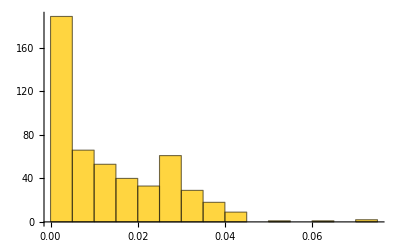
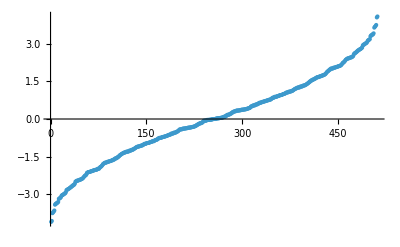

```mathematica
MeanLevelSpacingRatio[Sort[Chop[Eval]]]
{Histogram[Differences[Sort[Chop[Eval]]]],ListPlot[Sort[Chop[Eval]]]}
```

```mathematica
(* --- Initial pure state wavefunction vector setup --- *)
bellState = {0,1,1,0} / Sqrt[2.];
psiChain  = coherentstate[QubitStateFromBlochVector[1., 0], L];
(* Build the full combined position-basis initial vector *)
psi0      = BuildInitialStateVector[bellState, psiChain, L];
(* 4x4 Reference density matrix for boundary spin survival *)
rhoABref  = Outer[Times, bellState, Conjugate[bellState]];
```

## Computation

```mathematica
(* ================================================================ *)
(* BLOCK 10 – Energy Basis Wavefunction Projection                  *)
(* ================================================================ *)
Clear[psiE0, probE];
psiE0 = Evec . psi0;       (* Project initial wavefunction into the energy basis *)
probE = Abs[psiE0]^2;      (* Precompute probability weights for survival overlap *)
```

```mathematica
(* ================================================================ *)
(* BLOCK 11 – Parallel Kernel Object Distribution                   *)
(* ================================================================ *)
DistributeDefinitions[
  Eval, Evec, psiE0, probE, rhoABref, L,
  GetRhoAB, ComputeAllObservables, TraceOutA, TraceOutB, 
  VNEntropy2x2, VNEntropy4x4, Concurrence, spinFlip
];
```

```mathematica
(* ================================================================ *)
(* BLOCK 12 – Wavefunction Time Evolution Loop                      *)
(* ================================================================ *)
tMax=300.;
dt=0.1;
tlist = Range[0., tMax, dt];
```

```mathematica
AbsoluteTiming[allResults = ParallelTable[
  Module[{psiEt, psiAbt, rhoAB, survGlobal, overlap, obs},
    (* 1. Evolve the wavefunction in the energy basis *)
    psiEt = Exp[(-I) * Eval * t] * psiE0;
    
    (* 2. Transform back to the position basis via U^Dagger . psi *)
    psiAbt = ConjugateTranspose[Evec] . psiEt;    
    
    (* 3. Extract the 4x4 reduced density matrix via fast pure-state partial trace *)
    rhoAB = GetRhoAB[psiAbt, L];    
    
    (* 4. Global survival probability calculated via absolute squared overlap *)
    overlap    = probE . Exp[(-I) * Eval * t];
    survGlobal = Abs[overlap]^2;    
    
    (* 5. Compute all 4x4 system spin observables *)
    obs = ComputeAllObservables[rhoAB, rhoABref];
    Join[<|"Time" -> t, "SurvivalGlobal" -> survGlobal|>, obs]
  ],
  {t, tlist},
  DistributedContexts -> None
];]
```

{4.02331,Null}

## Results

```mathematica
(* ================================================================ *)
(* BLOCK 13 – Result extraction                                     *)
(* ================================================================ *)
Clear[ExtractTimeSeries];
ExtractTimeSeries[key_] :=
  {#["Time"], #[key]} & /@ allResults;
allResults[[1]]
```

<|Time→0.,SurvivalGlobal→1.,Concurrence→1.,Purity→1.,EntropyA→0.693147,EntropyB→0.693147,MutualInfo→1.38629,SpinSurvival→1.|>

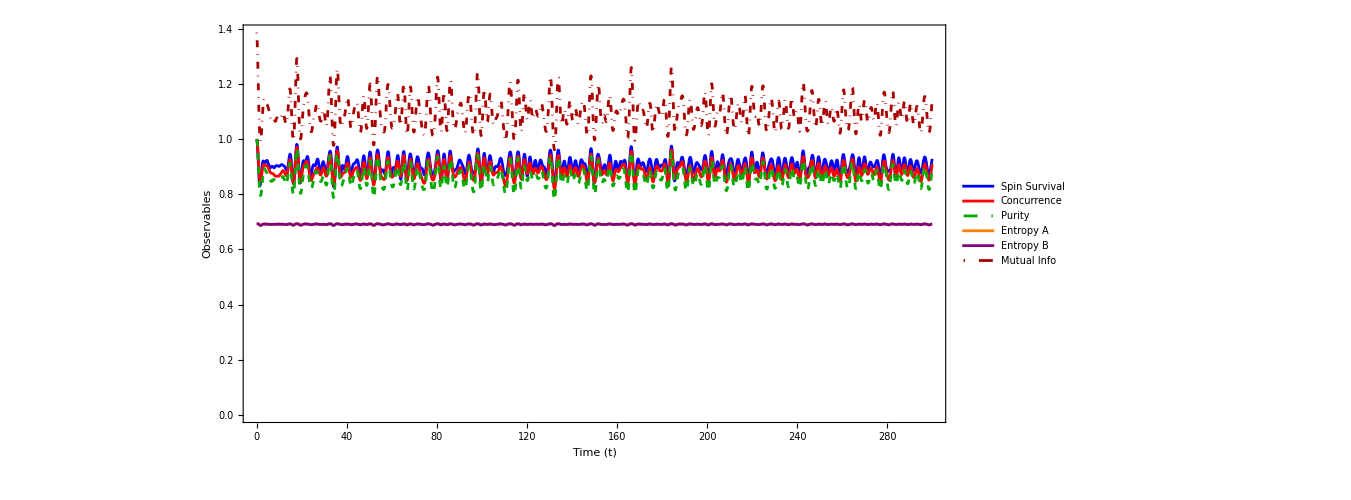

```mathematica
ListLinePlot[
  {ExtractTimeSeries["SpinSurvival"],
   ExtractTimeSeries["Concurrence"],
   ExtractTimeSeries["Purity"],
   ExtractTimeSeries["EntropyA"],
   ExtractTimeSeries["EntropyB"],
   ExtractTimeSeries["MutualInfo"]},
  Frame -> True,
  FrameLabel -> {"Time (t)", "Observables"},
  LabelStyle -> Directive[Black, 16],
  PlotStyle -> {
    Directive[Thick, Blue],
    Directive[Thick, Red],
    Directive[Thick, Darker[Green], Dashed],
    Directive[Thick, Orange],
    Directive[Thick, Purple],
    Directive[Thick, Darker[Red], DotDashed]
  },
  PlotLegends -> Placed[
    LineLegend[
      {"Spin Survival", "Concurrence", "Purity",
       "Entropy A", "Entropy B", "Mutual Info"},
      LegendFunction -> Framed
    ],
    Right
  ],
  ImageSize -> 1000,
  AspectRatio -> 0.5
]
```

# new

```mathematica
(* ================================================================ *)
(* NEW INITIAL STATE: General Mixed Spins + Thermal Chain Ensemble   *)
(* ================================================================ *)

(* 1. Define your general mixed initial state for spins A and B (4x4 matrix) *)
(* Example: A Werner State with purity parameter pWerner *)
pWerner = 0.9;
bellState = {0, 1, 1, 0} / Sqrt[2.];
rhoAB0 = pWerner * Outer[Times, bellState, Conjugate[bellState]] + (1 - pWerner) * IdentityMatrix[4]/4.;
rhoABref = rhoAB0; (* Reference density matrix for survival *)

(* Diagonalize the initial 4x4 system state *)
{valsAB, vecsAB} = Eigensystem[N[rhoAB0]];

(* 2. Define the inverse temperature beta for the chain *)
beta = 0.5; (* 0 = Infinite T (maximally mixed), Large = Low T *)

(* Find the raw eigenvalues and eigenvectors of the chain Hamiltonian Ha *)
{valsChain, vecsChain} = Transpose[Sort[Transpose[Eigensystem[N[Ha]]]]];
weightsChain = Exp[-beta * (valsChain - Min[valsChain])];
weightsChain = weightsChain / Total[weightsChain];

(* 3. Perform Ensemble Decomposition with Thermal Truncation *)
thermalThreshold = 10^-5; (* Ignore states with negligible probability *)

activeStates = Reap[
  Do[
    If[weightsChain[[k]] > thermalThreshold,
      Do[
        If[Re[valsAB[[m]]] > 10^-10,
          Module[{pGlobal, psi0, psiE0},
            pGlobal = Re[valsAB[[m]] * weightsChain[[k]]];
            (* Build full system pure state vector layout (q1, c, q2) *)
            psi0 = BuildInitialStateVector[vecsAB[[m]], vecsChain[[k]], L];
            (* Project directly to full energy basis *)
            psiE0 = Evec . psi0;
            Sow[{pGlobal, psiE0}];
          ]
        ],
        {m, 1, 4}
      ]
    ],
    {k, 1, Length[valsChain]}
  ]
][[2, 1]];

Print["Total pure states to evolve in the ensemble: ", Length[activeStates]];

(* 4. Precompute global survival matrix representation *)
(* Tr[rho(0)rho(t)] can be computed via an ultra-fast D x D quadratic form *)
rhoE0Matrix = Sum[item[[1]] * Outer[Times, item[[2]], Conjugate[item[[2]]]], {item, activeStates}];
absRhoE2 = Abs[rhoE0Matrix]^2; 
Clear[rhoE0Matrix];
```

Eigensystem::arh: Because finding 128 out of the 128 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

Total pure states to evolve in the ensemble: 512

```mathematica
(* 5. Distribute updated objects to parallel kernels *)
DistributeDefinitions[
  Eval, Evec, activeStates, absRhoE2, rhoABref, L,
  GetRhoAB, ComputeAllObservables, TraceOutA, TraceOutB, 
  VNEntropy2x2, VNEntropy4x4, Concurrence, spinFlip
];
```

```mathematica
(* ================================================================ *)
(* OPTIMIZED PRECOMPUTATION: Vectorizing the Ensemble               *)
(* ================================================================ *)
Nstates = Length[activeStates];

(* Combine all vectors into columns of a dense matrix, pre-weighted by Sqrt[weight] *)
PsiE0Mat = Transpose[Table[Sqrt[item[[1]]] * item[[2]], {item, activeStates}]];
Udag = ConjugateTranspose[Evec];

(* Distribute the new packed matrix structures to parallel kernels *)
DistributeDefinitions[
  Eval, Udag, PsiE0Mat, absRhoE2, rhoABref, L, Nstates,
  ComputeAllObservables, TraceOutA, TraceOutB, 
  VNEntropy2x2, VNEntropy4x4, Concurrence, spinFlip
];
```

```mathematica
(* ================================================================ *)
(* OPTIMIZED TIME EVOLUTION LOOP: Fully Vectorized                  *)
(* ================================================================ *)
tMax = 300.;
dt = 0.1;
tlist = Range[0., tMax, dt];

AbsoluteTiming[allResults = ParallelTable[
  Module[{phaseVec, PsiEtMat, PsiAbtMat, M, rhoAB, survGlobal, obs},
    (* 1. Precompute the phase factor vector for this time step *)
    phaseVec = Exp[(-I) * Eval * t];
    
    (* 2. Mixed state global survival probability via fast quadratic form *)
    survGlobal = Re[Conjugate[phaseVec] . (absRhoE2 . phaseVec)];
    
    (* 3. Evolve all 512 states simultaneously *)
    PsiEtMat = phaseVec * PsiE0Mat;
    
    (* 4. Transform all states to position basis at once via dense BLAS *)
    PsiAbtMat = Udag . PsiEtMat;
    
    (* 5. Multi-state partial trace and ensemble average using index maps *)
    M = ArrayReshape[
      Transpose[ArrayReshape[PsiAbtMat, {2, 2^L, 2, Nstates}], {1, 3, 2, 4}],
      {4, 2^L * Nstates}
    ];
    rhoAB = M . ConjugateTranspose[M];
    
    (* 6. Compute all 4x4 system observables exactly as before *)
    obs = ComputeAllObservables[rhoAB, rhoABref];
    Join[<|"Time" -> t, "SurvivalGlobal" -> survGlobal|>, obs]
  ],
  {t, tlist},
  DistributedContexts -> None
];]
```

{29.9524,Null}

## Results

```mathematica
(* ================================================================ *)
(* BLOCK 13 – Result extraction                                     *)
(* ================================================================ *)
Clear[ExtractTimeSeries];
ExtractTimeSeries[key_] :=
  {#["Time"], #[key]} & /@ allResults;
allResults[[1]]
```

<|Time→0.,SurvivalGlobal→0.00801629,Concurrence→0.85,Purity→0.8575,EntropyA→0.693147,EntropyB→0.693147,MutualInfo→1.03751,SpinSurvival→0.8575|>

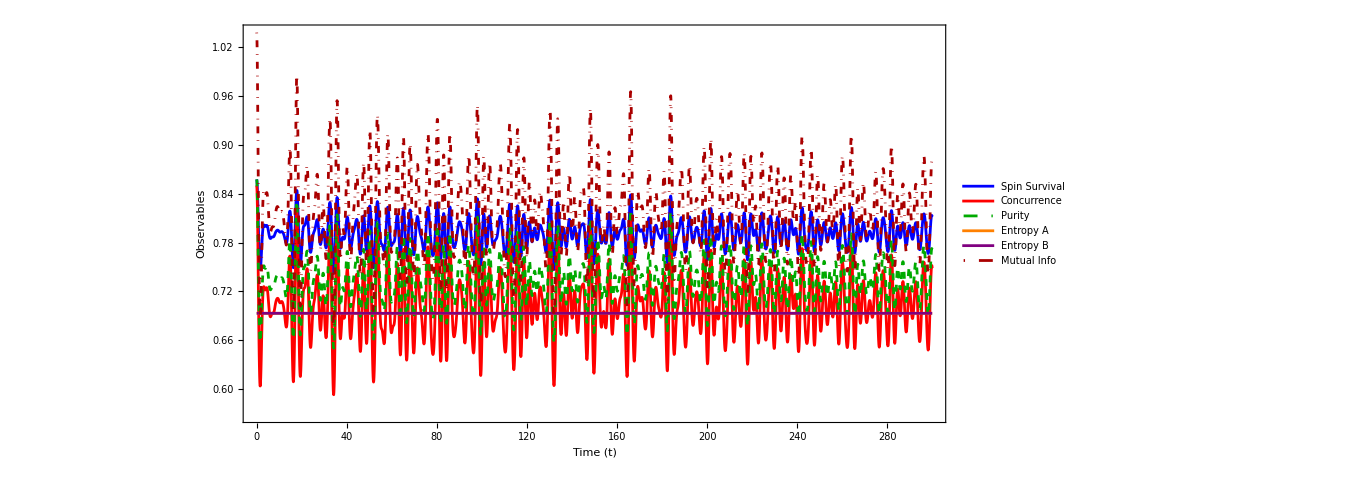

```mathematica
ListLinePlot[
  {ExtractTimeSeries["SpinSurvival"],
   ExtractTimeSeries["Concurrence"],
   ExtractTimeSeries["Purity"],
   ExtractTimeSeries["EntropyA"],
   ExtractTimeSeries["EntropyB"],
   ExtractTimeSeries["MutualInfo"]},
  Frame -> True,
  FrameLabel -> {"Time (t)", "Observables"},
  LabelStyle -> Directive[Black, 16],
  PlotStyle -> {
    Directive[Thick, Blue],
    Directive[Thick, Red],
    Directive[Thick, Darker[Green], Dashed],
    Directive[Thick, Orange],
    Directive[Thick, Purple],
    Directive[Thick, Darker[Red], DotDashed]
  },
  PlotLegends -> Placed[
    LineLegend[
      {"Spin Survival", "Concurrence", "Purity",
       "Entropy A", "Entropy B", "Mutual Info"},
      LegendFunction -> Framed
    ],
    Right
  ],
  ImageSize -> 1000,
  AspectRatio -> 0.5
]
```